```mathematica
Lab2, Маевский Александр, ПО-4
Задание 1
```

```mathematica
1. Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них дб рациональным выражением
```

```mathematica
{{t1=(5*(x^3+ 1)*(x^3-y^3))/((11*x^3-3)*(x-y))+(x+y)^2+x^3+y^3;
Expand[t1]  (*раскрывает скобки и степени выражения*)
(* -Graphics-
*)}, {□}}
```

{{Null (x^2+x^3+(5 x^3)/((-3+11 x^3) (x-y))+(5 x^6)/((-3+11 x^3) (x-y))+2 x y+y^2+y^3-(5 y^3)/((-3+11 x^3) (x-y))-(5 x^3 y^3)/((-3+11 x^3) (x-y)))},{□}}

```mathematica
ExpandAll[t1] (*расскрывает все скобки и все степени в любой части выражения*)
(* -Graphics- *)
```

t1

```mathematica
Factor[t1] (*раскладывает на целые числа*)
(* -Graphics- 
-Graphics-
Factor[1+2x+x^2]
(1+x)^2
*)
```

(2 x^2-3 x^3+16 x^5+11 x^6-x y+27 x^4 y+2 y^2+16 x^3 y^2-3 y^3+11 x^3 y^3)/(-3+11 x^3)

```mathematica
Together[t1] (*приводит к общему знаменателю и отменяет расложения*)
(* -Graphics- *)
```

(2 x^2-3 x^3+16 x^5+11 x^6-x y+27 x^4 y+2 y^2+16 x^3 y^2-3 y^3+11 x^3 y^3)/(-3+11 x^3)

```mathematica
Apart[t1]
(* -Graphics- 
дробь,содержащая лишь числитель и знаменатель,называется простой.
2 3/5-смешанная
*)
```

(x^2 (2-3 x+16 x^3+11 x^4))/(-3+11 x^3)+(x (-1+27 x^3) y)/(-3+11 x^3)+(2 (1+8 x^3) y^2)/(-3+11 x^3)+y^3

```mathematica
Cancel[t1] (*сокращает дробь/убирает общие множители в числителе и знаменателе выражения expr.*)
(* -Graphics- *)
```

x^3+y^3+(x+y)^2+(5 (1+x^3) (x^2+x y+y^2))/(-3+11 x^3)

```mathematica
Simplify[t1] (*упрощает выражение*)
(* -Graphics- *)
```

x^3+y^3+(x+y)^2+(5 (1+x^3) (x^2+x y+y^2))/(-3+11 x^3)

## 2

```mathematica
t2=Numerator[Together[t1]];(*Numerator - выделяет числитель together - приводит к общему знаменателю без together выведет все выражение (будет считать, что все делит на 1) *)
t2
```

2 x^2-3 x^3+16 x^5+11 x^6-x y+27 x^4 y+2 y^2+16 x^3 y^2-3 y^3+11 x^3 y^3

```mathematica
Collect[t2,x] (*собирает вместе термины,включающие одинаковые степени объектов,соответствующих x.*)
(* -Graphics- *)
```

2 x^2+16 x^5+11 x^6-x y+27 x^4 y+2 y^2-3 y^3+x^3 (-3+16 y^2+11 y^3)

```mathematica
Collect[t2,y]
```

2 x^2-3 x^3+16 x^5+11 x^6+(-x+27 x^4) y+(2+16 x^3) y^2+(-3+11 x^3) y^3

```mathematica
Exponent[t2,y](*дает максимальную степень,с которой форма появляется в расширенной форме expr*)
Exponent[t2,x]
(* -Graphics- *)
```

3

6

```mathematica
Coefficient[t2,x,2] (*дает коэффициент формы в многочлене expr*)
(* -Graphics- 
{{, Coefficientpaclet:ref/Coefficient[expr,form,n]
gives the coefficient of form^n in expr.}}
*)
(* берет все члены с х^2 и выводит их коэффициенты *)
```

2

```mathematica
Задание 2
```

```mathematica
D[x^n*Cos[x], x]
(*-Graphics-*)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

```mathematica
(* {{Dpaclet:ref/D[f,x]
gives the partial derivative ∂f/∂x.}, {Dpaclet:ref/D[f,{x,n}]
gives the multiple derivative ∂^n f/∂x^n.}} *)
```

```mathematica
D[(a*x^3+2*x^2),x]
```

4 x+3 a x^2

```mathematica
D[(4*x^2-5*x+8-3/x),{x,3}]
```

18/x^4

```mathematica
D[(x^3*y^2+3*x^2),{x,3},{y,2}]
```

12

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
firstResult = x^3/(x^2+1);
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
secondResult = Together[D[x^2/2-1/2 Log[1+x^2],x]](*складывает в сумму по общему знаменателю и отменяет множители в результате.*)
firstResult === secondResult
```

x^3/(1+x^2)

True

```mathematica
firstResult2 = 1/(x^3+1);
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
secondResult2 = Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]
firstResult2 == secondResult2
```

1/(1+x^3)

True

```mathematica
-Graphics-
(*
Integratepaclet:ref/Integrate[f,{x,Subscript[x, min],Subscript[x, max]}]gives the definite integral∫_Subscript[x, min]^Subscript[x, max] f dx.
*)
```

```mathematica
Integrate[5*x-2*√x+32/x^3, {x,1,4}]
```

259/6

```mathematica
(*
-Graphics-
-Graphics-
*)
```

```mathematica
N[Integrate[(1+x^4)^(1/3), {x,0,1}],25](*N даёт численное значение*)
```

1.057527731779011858114859

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

```mathematica
Задание 3
```

```mathematica
(*
-Graphics-
Solvepaclet:ref/Solve[expr,vars]
пытается решить систему уравнений или неравенств для переменных варс 
 *)
```

```mathematica
Solve[a*x^4+x^2+3==0, x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

```mathematica
(*
-Graphics-
*)
```

```mathematica
Solve[x^2+y==1 && y^2-x^2==2,{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

```mathematica
(*
```

```mathematica
Solve[x^2+a x+1==0,x]
{{x->1/2 (-a-√(-4+a^2))},{x->1/2 (-a+√(-4+a^2))}}
NSolve[x^2+a x+1==0,x](*попытки найти численные аппроксимации решений системы expr уравнений или неравенств для переменных vars.*)
{{x->0.5 (-1. a-1. √(-4.+a^2))},{x->0.5 (-1. a+√(-4.+a^2))}}
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

{{x→0.5 (-1. a-1. √(-4.+a^2))},{x→0.5 (-1. a+√(-4.+a^2))}}

{{x→0.5 (-1. a-1. √(-4.+a^2))},{x→0.5 (-1. a+√(-4.+a^2))}}

```mathematica
Solve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→5-(Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025)^3,y→Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025},{x→5-(Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715)^3,y→Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715},{x→5-(Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702)^3,y→Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702},{x→5-(Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702)^3,y→Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702},{x→5-(Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017)^3,y→Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017},{x→5-(Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017)^3,y→Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017}}

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y},Reals]
(* численное решение уравнения *)
```

{{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285}}

```mathematica
result = DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x](*решает дифференциальное уравнение для функции u с независимой переменной*)
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
result2 = DSolve[y'[x]+y[x]*Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

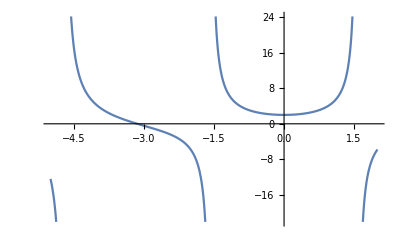

```mathematica
Plot[Evaluate[y[x]/. result /. {C[1] ->1}],{x,-5,2}] (*/. - ReplaceAll*)
```

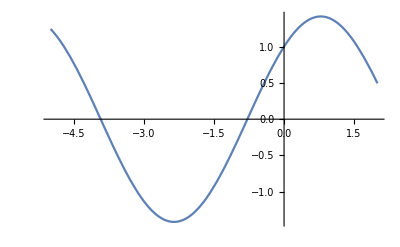

```mathematica
Plot[Evaluate[y[x]/. result2 /. {C[1] ->1}],{x,-5,2}]
```

```mathematica
t3= DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==2, y'[0]==3}, y[x], x]//FullSimplify
(*DSolve[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]*)
(*
находит численное решение уравнения обыкновенных дифференциальных уравнений для функции u с независимой переменной x в диапазоне от Subscript[x,min] до Subscript[x,max].
*)
```

{{y[x]→2 ⅇ^(x/2) π (-((AiryAi[1/4]+AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+AiryBiPrime[1/4]))}}

```mathematica
t4 = NDSolve[{y''[x]-y'[x]+x* y[x]==0, y[0]==2, y'[0]==3}, y[x], {x, -5,5}] (*находит численное решение уравнения обыкновенных дифференциальных уравнений для функции u с независимой переменной x в диапазоне от Subscript[x,min] до Subscript[x,max].*)
(* численное решение дифф уравнения *)
```

```mathematica
{{y[x]->InterpolatingFunction[…][x]}} (*представляет собой приближенную функцию,значения которой находятся интерполяцией*)
```

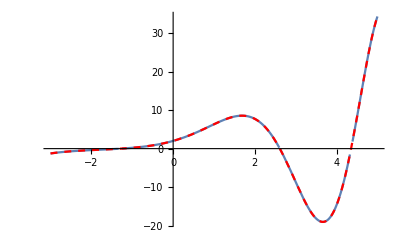

```mathematica
Show[Plot[t3[[1,1,2]],{x,-3,5}], Plot[t4[[1, 1, 2]], {x, -3, 5},PlotStyle->{Dashed, Red}]]
```